## Elliptic Curves

```mathematica
ellip[A_,B_]:=(x^3+A x+B)^(1/2)
delt[A_,B_]:=-16(4 A^3-27 B^2)
DynamicModule[{A=0,B=0},Column[{
Dynamic@ellip[A,B],
Dynamic@delt[A,B],
Dynamic@Plot[{ellip[A,B],-ellip[A,B]},{x,-10,10},PlotStyle-> {Red,Red},ImageSize-> {450},PlotRange->All],
Row[{Slider[Dynamic[A],{-100,100}],,Dynamic@A}],
Row[{Slider[Dynamic[B],{-100,100}],,Dynamic@B}]}
]
]
```

```mathematica
ellip[A_,B_]:=(x^3+A x+B)^(1/2)
delt[A_,B_]:=-16(4 A^3-27 B^2)
DynamicModule[{A=0,B=0},Column[{
Dynamic@ellip[A,B],
Dynamic@delt[A,B],
Dynamic@Plot3D[{ellip[A,B],-ellip[A,B]},{x,-10,10},{A,-50,50},PlotStyle-> {Red,Red},ImageSize-> {450},PlotRange->All,BoxRatios->Automatic,AxesLabel->{x,"A",y}],
Row[{Slider[Dynamic[B],{-100,100}],,Dynamic@B}]}
]
]
```

```mathematica
Solve[0==(4 3^3-27 B^2),B]
```

{{B→-2},{B→2}}

## Group Operation

### Given two points: P=(x_1,y_1), Q=(x_2,y_2) We need to find the points that intersect the line y=s x+m ·We square and equate: (s x + m)^2=s^2 x^2+2 s x m +m^2=x^3+a x +b ·The slope s is: s=(y_2-y_1)/(x_2-x_1) ·The y-intercept: m=y_1-(y_2-y_1)/(x_2-x_1)x_1 ·Substituting: ((y_2-y_1)/(x_2-x_1))^2 x^2+2 x((y_2-y_1)/(x_2-x_1)) (y_1-(y_2-y_1)/(x_2-x_1)x_1) +(y_1-(y_2-y_1)/(x_2-x_1)x_1)^2=x^3+a x +b ·Rearranging: x^3+[-((y_2-y_1)/(x_2-x_1))^2]x^2+[a-2 ((y_2-y_1)/(x_2-x_1)) (y_1-(y_2-y_1)/(x_2-x_1)x_1)]x+[b-(y_1-(y_2-y_1)/(x_2-x_1)x_1)^2]=0 ·We already know two solutions:

```mathematica
Solve[x^3+(-(Subscript[y, 2]-Subscript[y, 1])/(Subscript[x, 2]-Subscript[x, 1]))x^2+(a-2((Subscript[y, 2]-Subscript[y, 1])/(Subscript[x, 2]-Subscript[x, 1]))(Subscript[y, 1]-(Subscript[y, 2]-Subscript[y, 1])/(Subscript[x, 2]-Subscript[x, 1])Subscript[x, 1]))x+(b-(Subscript[y, 1]-(Subscript[y, 2]-Subscript[y, 1])/(Subscript[x, 2]-Subscript[x, 1])Subscript[x, 1])^2)==0,x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[b+x^3-(x^2 (-y_1+y_2))/(-x_1+x_2)-(y_1-(x_1 (-y_1+y_2))/(-x_1+x_2))^2+x (a-(2 (-y_1+y_2) (y_1-(x_1 (-y_1+y_2))/(-x_1+x_2)))/(-x_1+x_2))==0,x]

### ??????????????????? ·We end up with: ·x_3=s^2-x_1-x_2 mod p ·y_3=s(x_1-x_3)-y_1 mod p where s={(y_2-y_1)/(x_2-x_1)mod p; if P ≠ Q (3 x_1^2+a)/(2 y_1)mod p; if P=Q

## Identity element and inverses

### P+O = P ∀P, where O is a point at infinity P+P^-1=O, where P^-1=(x,-y)

### The points in an EC, including O, have cyclic subgroups. Under certain conditions, all points form a cyclic group.

## Example of cycle:

### E:y^2=x^3+2 x+2 mod 17 Starting with P=(5,1): 2P: s=(2(1))^-1(3(5)^2+2)≡13mod 17 x_3=(13)^2-5-5≡6mod 17 y_3=13(5-6)-1≡3mod 17 2P=(6,3)

```mathematica
eladd[P_,Q_,p_,a_]:=(
s=If[P==Q,Mod[(3 P⟦1⟧^2+a)ModularInverse[2 P⟦2⟧,p],p],Mod[(Q⟦2⟧-P⟦2⟧)ModularInverse[Q⟦1⟧-P⟦1⟧,p],p]];
x=Mod[s^2-P⟦1⟧-Q⟦1⟧,p];
y=Mod[s(P⟦1⟧-x)-P⟦2⟧,p];
{x,y}
)
```

```mathematica
eladd[{6,3},{5,1},17,2]
```

{10,6}

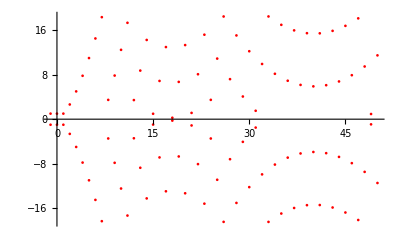

ModularEC_-1_1_19.jpg

```mathematica
(*a = 6277101735386680763835789423207666416083908700390324961276; 
b = 2455155546008943817740293915197451784769108058161191238065;
p = 6277101735386680763835789423207666416083908700390324961279;*)
a = -1;
b = 1;
p = 19;
dp = DiscretePlot[{Mod[ellip[a,b],p],-Mod[ellip[a,b],p]},{x,-49,50},PlotStyle-> {Red,Red},Filling-> None, ImageSize-> {700},PlotRange->All]
Export["ModularEC_-1_1_19.jpg",dp]
```

{-1,1}

{1,1}

{0,4}

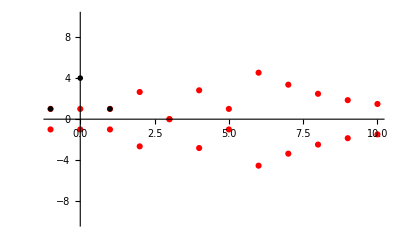

ECop.jpg

ModularInverse::minv: The two arguments to ModularInverse must be ordinary or Gaussian integers.

{Mod[1.5+Mod[0.172604 ModularInverse[0.5,7],7]^2,7],Mod[-1+(-1-Mod[1.5+Mod[0.172604 ModularInverse[0.5,7],7]^2,7]) Mod[0.172604 ModularInverse[0.5,7],7],7]}

```mathematica
a = -1;
b = 1;
x1 = -1;
x2=1;
y1 = (x1^3+a x1+b)^(1/2);
y2 = (x2^3+a x2+b)^(1/2);
P = {x1,y1}
Q = {x2,y2}
R =eladd[P,Q,5,a]
pl = Show[{
DiscretePlot[{Mod[ellip[a,b],5],-Mod[ellip[a,b],5]},{x,-10,10},PlotStyle-> {Red,Red},Filling-> None, ImageSize-> {700},PlotRange->{-10,10}],
Graphics[{PointSize[.01],Point[P],Point[Q],Point[R]}]
}]
Export["ECop12312.jpg",pl]
```